```mathematica
eq1= x+y+z==4;
eq2=x^2-y^2-z==2;
eq3= -x + 6y -z == -2;

sol= Solve[{eq1,eq2,eq3},{x,y,z}]
```

{{x→1/14 (-7-√1185),y→2/7,z→1/14 (59+√1185)},{x→1/14 (-7+√1185),y→2/7,z→1/14 (59-√1185)}}

```mathematica
solz1= z/.Solve[eq1, z];
solz2= z/.Solve[eq2, z];
solz3= z/.Solve[eq3, z];

Plot3D[{solz1,solz2,solz3},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
(*------------------------*)
```

```mathematica
Delta[i_,j_]:= If[ i===j,1,0];
lz={{1,0,0},{0,0,0},{0,0,-1}}//MatrixForm;
lp[i_,j_]:=Sqrt[2] Delta[i, j+1];
lm[i_,j_]:=Sqrt[2] Delta[i, j-1];

Lx=lx[i_,j_]=Table[ 1/2(lp[i,j] + lm[i,j]), {i,-1,1},{j,-1,1}]//MatrixForm;
Ly=ly[i_,j_]=Table[ 1/2 /I(lp[i,j] - lm[i,j]), {i,1,3},{j,1,3}]//MatrixForm;


Print[" Lx =  " , Lx , "  ,   Ly =  " , Ly  , "  , Lz = " , lz]
```

Lx =  (0 | 1/(√2) | 0
1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0)  ,   Ly =  (0 | ⅈ/(√2) | 0
-ⅈ/(√2) | 0 | ⅈ/(√2)
0 | -ⅈ/(√2) | 0)  , Lz = (1 | 0 | 0
0 | 0 | 0
0 | 0 | -1)

```mathematica
(*-----------------------*)
```

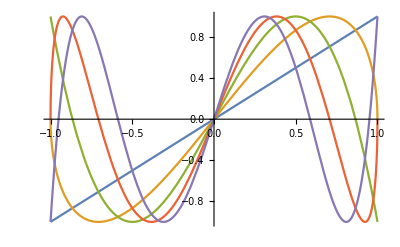

```mathematica
soluz[n_]=y[x]/.DSolve[(1-x^2) y''[x] - x y'[x] + (n^2) y[x] == 0 , y[x] , x];
soluz[n_]=soluz[n]/.{C[1]->0, C[2]->1};
Plot[Evaluate[Table[soluz[n], {n,1,5}]],{x,-1,1}]
```

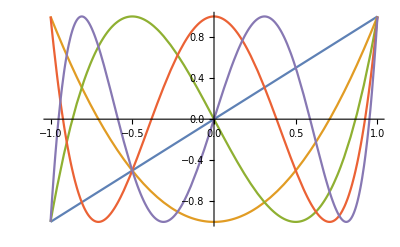

```mathematica
T[0,x_]=1;
T[1,x_]=x;
T[n_,x]:=Expand[ 2 x T[n-1,x] - T[n-2,x]];
primi5=Table[ T[i,x],{i,1,5}];
Plot[primi5 , {x,-1,1}]
```